```mathematica
k[t_]:=140.62+112.14 10^-4 t;
kl[t_]:=45.43+26 10 ^-3 t;
ksl[t_]:= 2430.3-191.61 10^-2 t; 
kt[t_]:= Piecewise[{{k[t],298<t ≤1188} ,{kl[t],t ≥ 1228},{ ksl[t],1188<t<1228}}];
Plot[kt[t],{t,200,2000}]
```

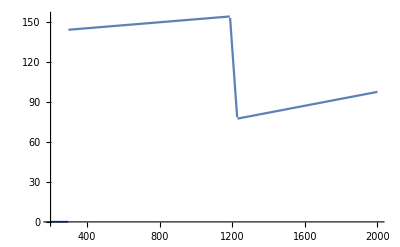

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\kBronze.xlsx",Table[{kt[t],t},{t,300,2000,50}]] ;
```

```mathematica
ζ[t_,Tm_,Ts_]:=(t-Ts)/(Tm-Ts);
Ut[θ_,Tm_,Ts_]:=(ζ[θ,Tm,Ts])^3(10-15 ζ[θ,Tm,Ts]+6 ζ[θ,Tm,Ts]^2);
dUt[θ_]=D[Ut[θ],θ];
```

```mathematica
ksmooth[t_]:= k[t](1-Ut[t,1228,1188])+kl[t]Ut[t,1228,1188];
```

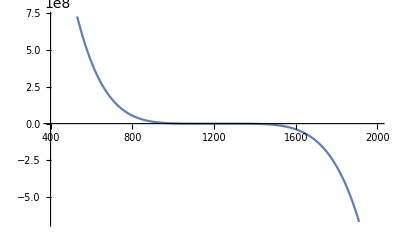

```mathematica
Plot[ksmooth[t],{t,400,2000}]
```

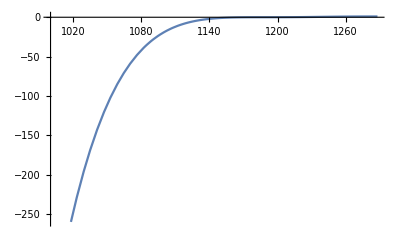

```mathematica
Plot[Ut[θ,1288,1188],{θ,1000,1288}]
```

This data are valid for the Cu-Al (bronze) so it can be that is different from the 70Cu-30Zn case.

```mathematica
ρ[t_]:= 7262 - 48.6 10^-2 (t-298);
ρl[t_]:= 6425- 65 10^-2(t-1350);
```

```mathematica
ρt[t_]:=Piecewise[{{ρ[t],298≤ t≤1350 },{ρl[t],t>1350}}]
```

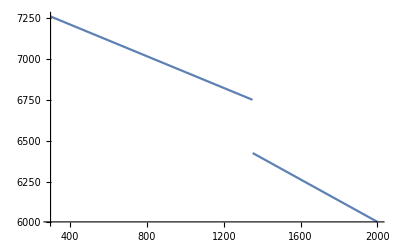

```mathematica
Plot[ρt[t],{t,298,2000}]
```

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\rhpBronze.csv",Table[{N@ρt[t]*10^-12,t},{t,300,2000,50}]]
```

C:\Users\tonii\OneDrive\Documents\GitHub\Mathematica\rhpBronze.csv

```mathematica
kp[t_] := Piecewise[{{k[t]*0.1,298<t ≤1188} ,{kl[t],t ≥ 1228},{ ksl[t],1188<t<1228}}];
```

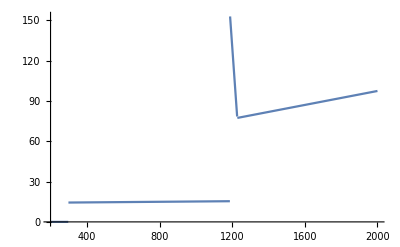

```mathematica
Plot[kp[t],{t,200,2000}]
```

Make the smooth transition to the conductivity of the liquid phase. We make transition region big as mushy zone. Could be better to calculate the threshold temperature for the sintering.

```mathematica
Tm = 1188; dT=200;
α[t_]:=1/2( 1+Tanh[4/dT*(t-Tm)]);
dα[t_]=D[α[t],t];
kpowder[t_]:=k[t]*0.1(1-α[t])+kl[t]*α[t];
```

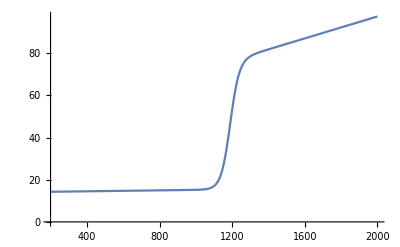

```mathematica
Plot[kpowder[t],{t,200,2000}]
```

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\kBronzePowder.csv",Table[{kpowder[t],t},{t,300,2000,50}]] ;
```